```mathematica
(* Problem 1 *)
```

```mathematica
ListN={1,2,-5,8,10,22,-5,-9,28}
```

{1,2,-5,8,10,22,-5,-9,28}

```mathematica
PosN[L_]:=Module[{Sum=0,i},For[i=1,i<=Length[L],i++,Sum=Sum+If[L[[i]]>0,L[[i]],0]]; Sum] (* Add only positive number *)
```

```mathematica
PosN[ListN]
```

71

```mathematica
(* Function Break *)
```

```mathematica
For[i=1,i<=6,i++,Print[i];If[i>2,{Print["Not OK"];Break[]},Print["OK"]]]
```

1

OK

2

OK

3

Not OK

```mathematica
(* Problem 2 *)
```

```mathematica
SumNon0[L_] := Module[{Sum = 0 ,i}, For [i = 1, i<= Length[L], i++, If[L[[i]] != 0, Sum = 1./L[[i]]+Sum ,Sum="∞";Break[]]];Sum] (* If there's 0 in the list return INF, but if not compute the formula *)
```

```mathematica
L1={1,0,15};
```

```mathematica
SumNon0[L1]
```

∞

```mathematica
L2={2,2,10,1}
```

{2,2,10,1}

```mathematica
SumNon0[L2]
```

2.1

```mathematica
(* Problem 3 *)
```

```mathematica
Clear[LP]
```

```mathematica
PrN1N2[N1_,N2_]:=Module[{i,L={},LP,plot},For[i=N1,i<=N2,i++,If[PrimeQ[i],L=Join[L,{i}]]];plot=ListPlot[L,PlotStyle->{Red,PointSize[0.015]}];{L,plot}]
```

```mathematica
LP=PrN1N2[10,201];
```

```mathematica
LP[[1]]
```

{11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199}

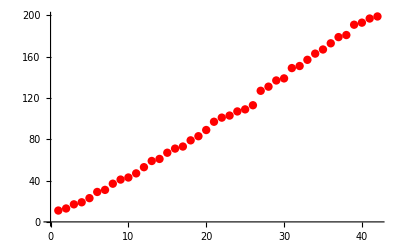

```mathematica
LP[[2]]
```

```mathematica
(* Problem 4 *)
```

```mathematica
fN[N_]:= Module[{i,L= 1}, For[i = 1,i<=N ,i++,If[PrimeQ[i], L++;]];L]
```

```mathematica
LN=Table[{i,fN[i]},{i,1,100}]
```

{{1,1},{2,2},{3,3},{4,3},{5,4},{6,4},{7,5},{8,5},{9,5},{10,5},{11,6},{12,6},{13,7},{14,7},{15,7},{16,7},{17,8},{18,8},{19,9},{20,9},{21,9},{22,9},{23,10},{24,10},{25,10},{26,10},{27,10},{28,10},{29,11},{30,11},{31,12},{32,12},{33,12},{34,12},{35,12},{36,12},{37,13},{38,13},{39,13},{40,13},{41,14},{42,14},{43,15},{44,15},{45,15},{46,15},{47,16},{48,16},{49,16},{50,16},{51,16},{52,16},{53,17},{54,17},{55,17},{56,17},{57,17},{58,17},{59,18},{60,18},{61,19},{62,19},{63,19},{64,19},{65,19},{66,19},{67,20},{68,20},{69,20},{70,20},{71,21},{72,21},{73,22},{74,22},{75,22},{76,22},{77,22},{78,22},{79,23},{80,23},{81,23},{82,23},{83,24},{84,24},{85,24},{86,24},{87,24},{88,24},{89,25},{90,25},{91,25},{92,25},{93,25},{94,25},{95,25},{96,25},{97,26},{98,26},{99,26},{100,26}}

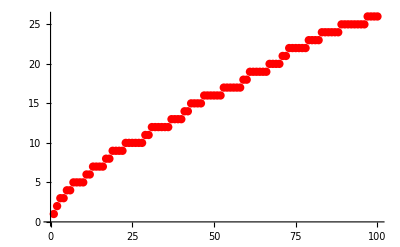

```mathematica
GfN=ListPlot[LN,PlotStyle->{Red,PointSize[0.015]}]
```

```mathematica
(* Let's interpolate using point {1,25,50,75,100} *)
```

```mathematica
InT=LN[[{1,25,50,75,100}]]
```

{{1,1},{25,10},{50,16},{75,22},{100,26}}

```mathematica
fQint=Interpolation[InT, Method->"Spline"]
```

InterpolatingFunction[…]

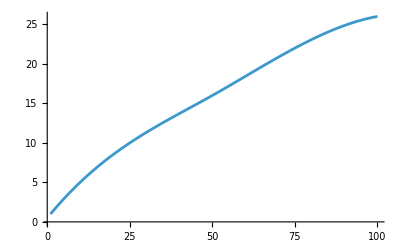

```mathematica
GF=Plot[fQint[t],{t,1,100}]
```

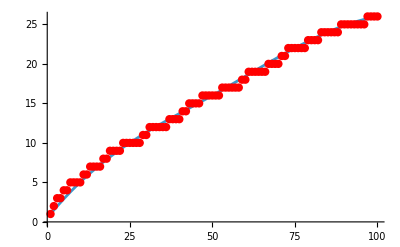

```mathematica
Show[GF,GfN]
```

```mathematica
(* Find the LSE *)
```

```mathematica
LN[[21]][[2]]
```

9

```mathematica
LSE = Sqrt[Sum[(fQint[i]-LN[[i]][[2]])^2,{i,100}]]
```

4.55751

```mathematica
(* Problem 5 *)
```

```mathematica
R1=3
```

3

```mathematica
f1[t_]:={R1*Cos[t],R1*Sin[t]+R1}
```

```mathematica
f2[t_]:={t,R1}
```

```mathematica
Tr1[t_]:=If[t>=0&&t<=2*Pi,f1[t],f2[t]]
```

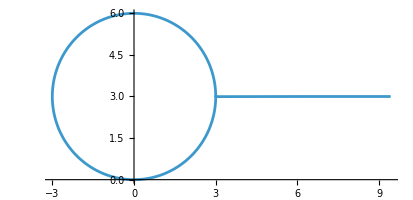

```mathematica
ParametricPlot[Tr1[t],{t,0,3*Pi},Exclusions->None]
```

```mathematica
(* Example of Which and check *)
```

```mathematica
F[x_]:=Which[x>0,1,x<0,2,x==0,3]
```

```mathematica
F[1]
```

1

```mathematica
F[-2]
```

2

```mathematica
F[0]
```

3

```mathematica
PrimePi[3]
```

2

```mathematica
F[x_]:=Which[x<0,f1[x],x<=5&&x>=0,f1[x],x>5,f1[x]]
```

```mathematica
F[1]
```

{3 Cos[1],3+3 Sin[1]}

```mathematica
(* Problem 5 Study and use the "Which" *)
```

```mathematica
Clear[t,f1,f2,f3,Tra5]
```

```mathematica
R1=3;
```

```mathematica
f1[t_]:={R1*Cos[t],R1*Sin[t]+R1} (* t>= 0 and t <= 2Pi *)
```

```mathematica
f2[t_]:={t,R1} (* t > 2Pi and t < 3Pi *)
```

```mathematica
f3[t_]:={R1*Cos[t]+R1+(3*Pi),R1*Sin[t]+R1} (* t >= 3Pi *)
```

```mathematica
Tra51[t_]:=Which[t>=0&&t<=2*Pi,f1[t],t>2*Pi&&t<3*Pi,f2[t],t>=3*Pi,f3[t]]
```

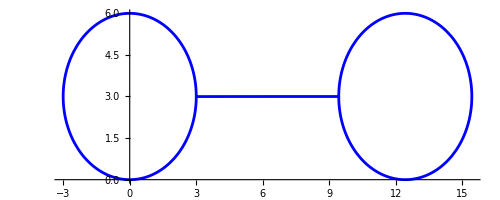

```mathematica
TwoCir=ParametricPlot[Tra51[t],{t,0,5*Pi},Exclusions->None,PlotStyle->Blue]
```

```mathematica
GDisk[t_] := Graphics[{Red,Disk[Tra51[t],0.5]}]
```

```mathematica
Tra51wDisk[t_]:=Show[TwoCir ,GDisk[t]]
```

```mathematica
Manipulate[Tra51wDisk[t],{t,0,5*Pi}]
```

```mathematica
(* Problem 6 *)
```

```mathematica
Ladder={{1,1},{5,5},{9,9},{13,13},{17,17},{21,21},{24,21},{28,17},{32,13},{36,9},{40,5}};
```

```mathematica
tmax=Max[Transpose[Ladder][[1]]]
```

40

```mathematica
fLadder=Interpolation[Ladder,InterpolationOrder->0]
```

InterpolatingFunction[…]

```mathematica
fL5[t_]:={t,fLadder[t]}
```

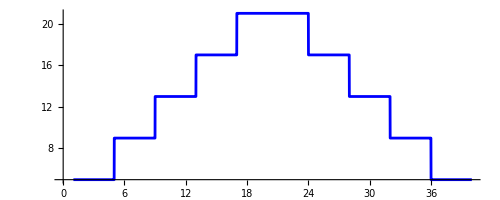

```mathematica
Tra5=ParametricPlot[fL5[t],{t,1,tmax},PlotStyle->Blue]
```

```mathematica
RR5 = 5
```

5

```mathematica
nreg=3
```

3

```mathematica
Clear[GP]
```

```mathematica
ObjectPol[s_]={Magenta,RegularPolygon[fL5[s],RR5,nreg]};
```

```mathematica
LadderwPoly[t_]:=Show[Tra5 ,Graphics[ObjectPol[t]]]
```

```mathematica
Manipulate[LadderwPoly[t],{t,1,tmax}]
```

```mathematica
(* Problem 7 *)
```

```mathematica
Clear[GPnew,GGPnew]
```

```mathematica
ObjectNew={Magenta,RegularPolygon[{0,0},RR5,nreg]}
```

{RGBColor[1, 0, 1],RegularPolygon[{0,0},5,3]}

```mathematica
ObjectRot[a_,s_]:=GeometricTransformation[ObjectNew,Composition[TranslationTransform[fL5[s]],RotationTransform[a]]]
```

```mathematica
GPnew[a_,s_]:=Graphics[ObjectRot[a,s],PlotRange->{{0,40},{-10,30}},Axes->True]
```

```mathematica
GGPnew[a_,s_]:=Show[GPnew[a,s],Tra5]
```

```mathematica
Manipulate[GGPnew[s,s],{s,1,tmax}]
```